```mathematica
Quit
```

## Find the paclet

```mathematica
If[$VersionNumber≥12.1,
PacletDirectoryLoad@FileNameJoin[{FileNameDrop@NotebookDirectory[],"COVID19"}],
PacletManager`PacletDirectoryAdd@FileNameJoin[{FileNameDrop@NotebookDirectory[],"COVID19"}]
];
```

```mathematica
<<COVID19`
```

## Growth Plots for US Counties

#### Choose some counties using anything that passes Interpreter[“USCounty”]

The first evaluation is very slow for importing and interpreting data, but subsequent evaluations are much faster

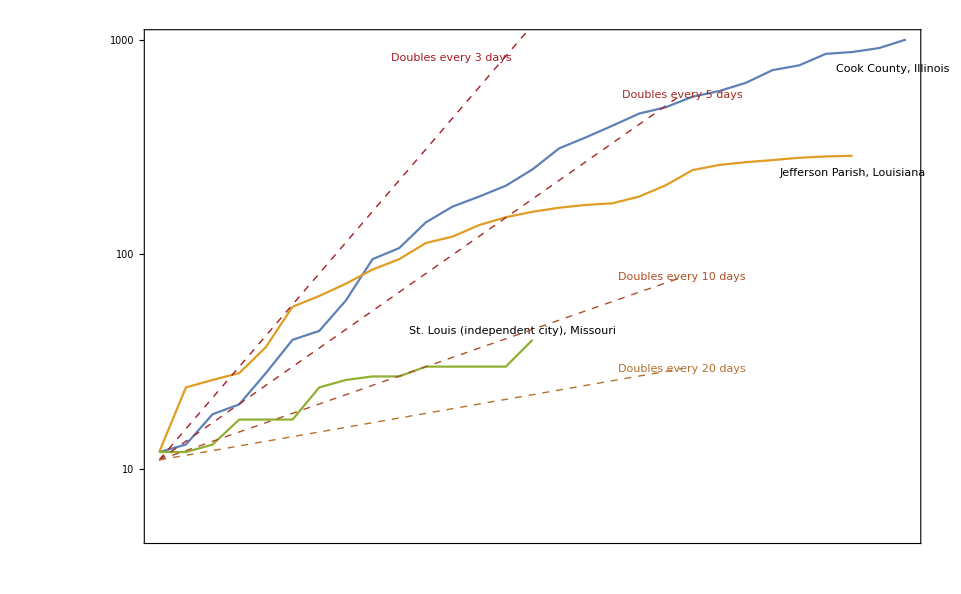

```mathematica
COVID19`USCountyGrowthPlot[{"Cook County, IL","Jefferson Parish, LA","St. Louis City"}]
```

#### Automatically choose the most affected counties

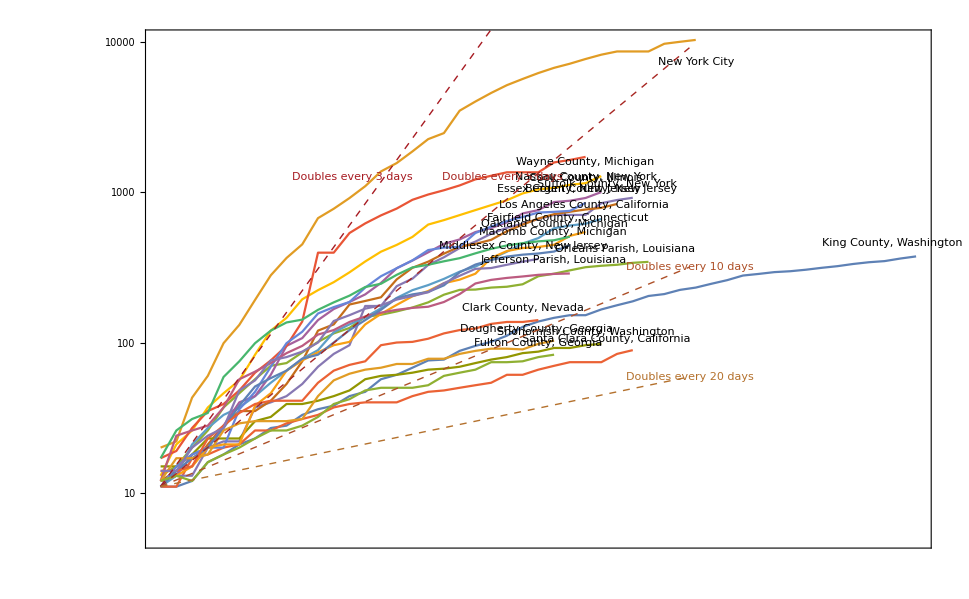

```mathematica
COVID19`USCountyGrowthPlot[]
```

## US State testing data

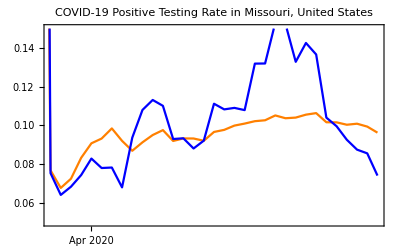
{-Graphics-,-Graphics-,}

```mathematica
COVID19`StateTestingPlots[Entity["AdministrativeDivision",{"Missouri","UnitedStates"}]]
```

## US Metro Area Plots and Data Table

#### I (Bob S) live in St. Louis, so I got this working. It should be easy to do the same for others metro areas.

```mathematica
{plots, table}=COVID19`MetroData["STL","MetroName"->"St. Louis ","ExtraPlots"->{p2,p1}];
```

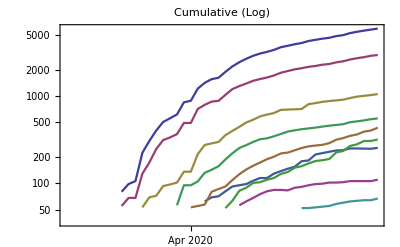
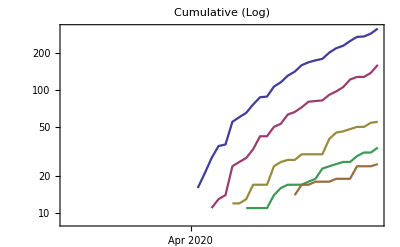
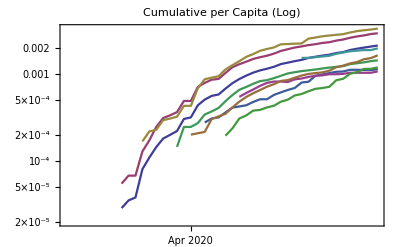
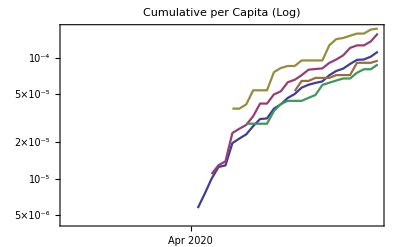
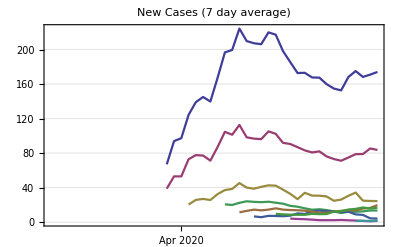
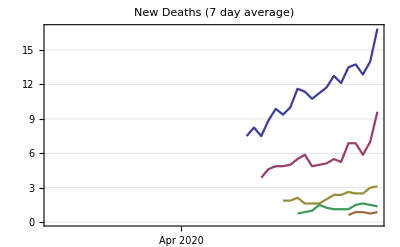
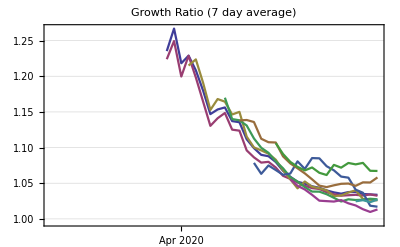
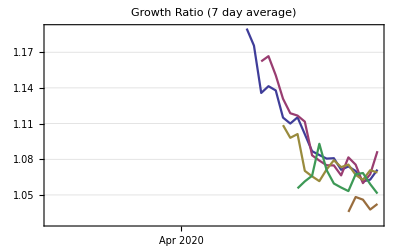
St. Louis Metro Area COVID-19 Timelines
From NY Times data on Tue 28 Apr 2020 |  | 
Cases (> 50) | Deaths (> 10) | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- |

```mathematica
plots
```

```mathematica
table
```

Tuesday 28 April 2020

#### Create a public web page with this info:

```mathematica
COVID19`DeployMetroData[{"STL",Entity["AdministrativeDivision",{"Missouri","UnitedStates"}]},"COVID19/STLMetro/TimelineGridAndDataTable","MetroName"->"St. Louis "]
SystemOpen[%]
```

CloudObject[https://www.wolframcloud.com/obj/bobs/COVID19/STLMetro/TimelineGridAndDataTable]

## Testing data

#### This source seems to have quality data, but I haven’t made TimeSeries yet.

```mathematica
testingdata=COVID19`OurWorldInDataTestingData["New"]
```

## Create Plots and Data Tables for Countries

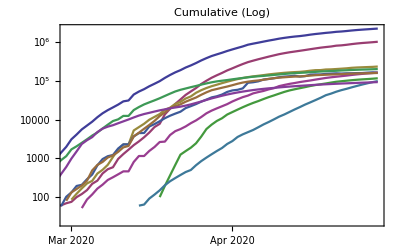
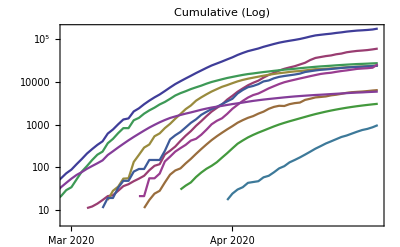
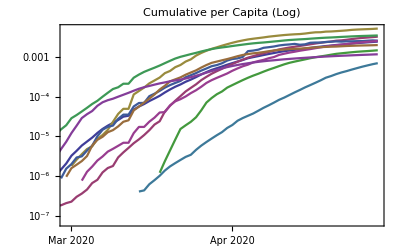
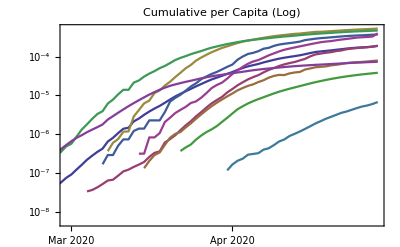
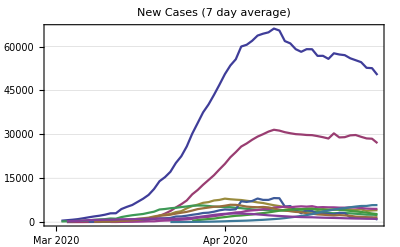
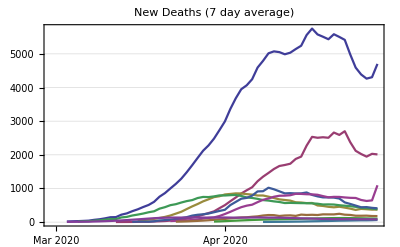
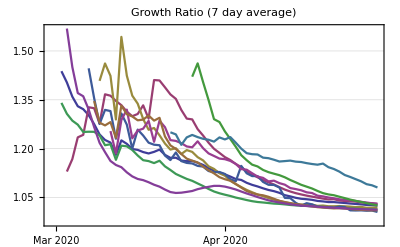
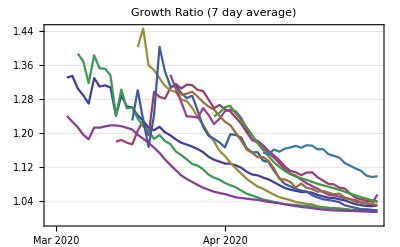
{COVID-19 Timelines
From NY Times data on Wed 29 Apr 2020 |  | 
Cases (> 50) | Deaths (> 10) | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | ,Wednesday 29 April 2020}

```mathematica
COVID19`CountryPlotsAndData[Automatic]
```

## Find Peaks

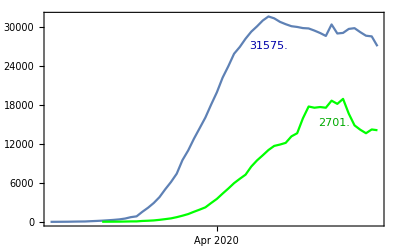
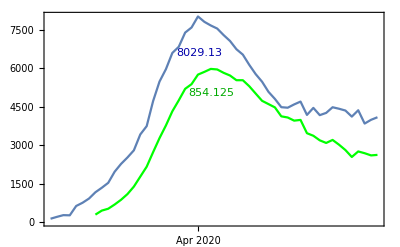
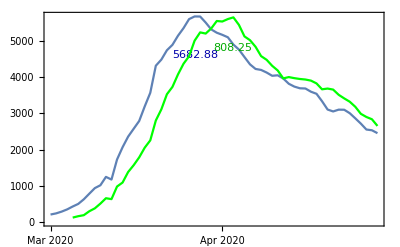
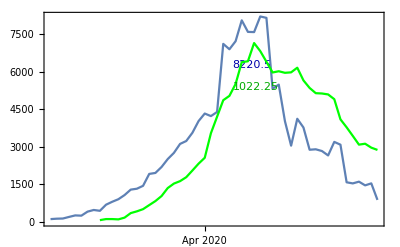
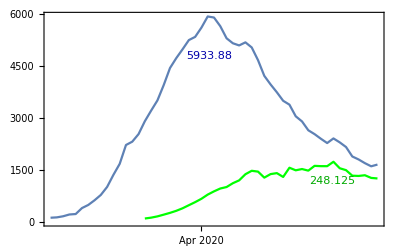
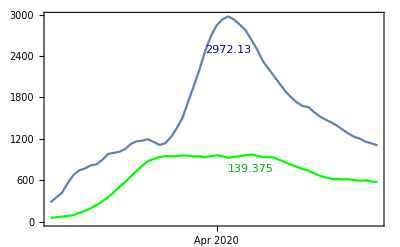
<|United States→-Graphics-,Spain→-Graphics-,Italy→-Graphics-,France→-Graphics-,Germany→-Graphics-,Iran→-Graphics-|>

```mathematica
COVID19`DailyPeakPlot[Automatic,"DeathValueMagnification"->7]
```